```mathematica
cols=Short[ColorData[97,"ColorList"],4];
extinction=Lighter[cols[[1,11]]]
coexistence=cols[[1,8]]
alleethreshold=cols⟦1,3⟧
preyonly=cols[[1,7]]
```

RGBColor[0.9433333333333334, 0.5549999999999999, 0.475]

RGBColor[1, 0.75, 0]

RGBColor[0.560181, 0.691569, 0.194885]

RGBColor[0.363898, 0.618501, 0.782349]

```mathematica
framelabels={Style["Predator mortality d",16],Style["Carrying capacity K",16]};
```

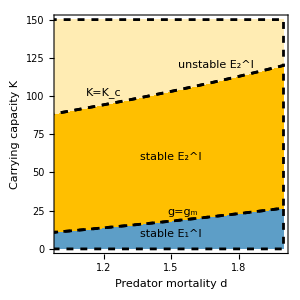

```mathematica
ρ=0.5;γ=0.1;α=0.7;τ=0.1;δ=0.15;
s1=μ>(α*δ*κ)/(1+γ*δ*κ);
s3=μ<α/γ;
s4=μ>(α*δ*κ)/(1+γ*δ*κ)-α/(γ*(1+γ*δ*κ));
i=RegionPlot[{s1,And[!s1,s3,s4],And[!s1,s3,!s4]},{μ,0.9,2},{κ,0,150},PlotRange->{{1,2},{0,150}},(*PlotPoints->60,MaxRecursion->10,*)BoundaryStyle->{Dashed,Black},PlotStyle->{preyonly,coexistence,Lighter[coexistence,0.7]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->framelabels,Epilog->{(*Style[Text["C",{1.95,140}],FontSize->16,Bold,Background->White],*)Style[Text["g=g_m",{1.55,24}],FontSize->10,Background->None],Style[Text["K=K_c",{1.2,102}],FontSize->10,Background->None],Style[Text["stable E_2^I",{1.5,60}],FontSize->10,Background->None],Style[Text["unstable E_2^I",{1.7,120}],FontSize->10,Background->None],Style[Text["stable E_1^I",{1.5,10}],FontSize->10,Background->None]},ImageSize->300]
```

```mathematica
F1[u_,v_]:=ρ*(1-u/κ)-(δ*v)/(1+δ*γ*u);
G[u_,v_]:=(α*δ*u)/(1+δ*γ*u)-μ;
```

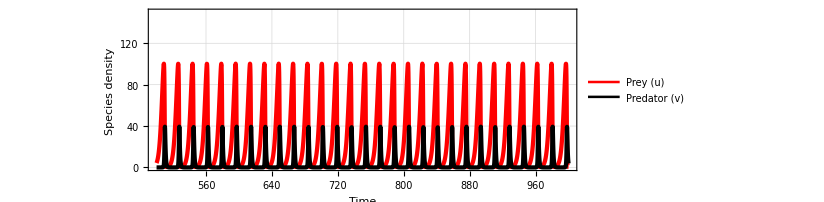

```mathematica
ρ=0.5;κ=150;δ=0.15;γ=0.1;α=0.7;μ=1.5;
sol=NDSolve[{u'[t]==u[t]*F1[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==3,v[0]==3},{u,v},{t,0,1000}];
A=Plot[Evaluate[{u[t],v[t]}/.sol],{t,500,1000},PlotRange->{{500,1000},{0,150}},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed],AspectRatio->1/3,Frame->True,PlotStyle->{{Red,Thickness[0.005]},{Black,Thickness[0.005]}},FrameStyle->Directive[Black,Thickness[0.0015]],FrameLabel->{Style["Time",16],Style["Species density",16]},PlotLegends->Placed[{"Prey (u)","Predator (v)"},{Right,Top}],ImageSize->610]
```

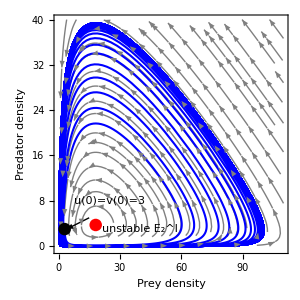

```mathematica
ρ=0.5;κ=150;δ=0.15;γ=0.1;α=0.7;μ=1.5;
data= Table[{{u,v},{u*F1[u,v],v*G[u,v]}},{u,0,110,1},{v,0,40,0.5}];
j=ListStreamPlot[data,StreamColorFunction->None,StreamStyle->Gray,PlotRange->{{0,110},{-0.5,40}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Prey density",16],Style["Predator density",16]},ImageSize->300];
{usol,vsol}={u[t],v[t]}/.Flatten[NDSolve[{u'[t]==u[t]*F1[u[t],v[t]],v'[t]==v[t]*G[u[t],v[t]],u[0]==3,v[0]==3},{u[t],v[t]},{t,0,2000}]];
k=ParametricPlot[{{usol,vsol}},{t,0,2000},AxesLabel->{"x","y"},PlotStyle->Directive[Blue,Thickness[0.005]],PlotPoints->2000,MaxRecursion->5];
solutions=Select[NSolve[{F1[x,y]==0,G[x,y]==0},{x,y}],FreeQ[#,Complex]&];
solutionPoints={x,y}/. solutions;
p1=Graphics[{Red,PointSize[0.03],Point[solutionPoints]}];
p2=Graphics[{Black,PointSize[0.03],Point[{3,3}]}];
p3=Graphics[Arrow[{{15,5},{4,3}}]];
A1=Show[j,k,p1,p2,p3,Epilog->{Style[Text["unstable E_2^I",{40,3}],FontSize->14,Background->White],Style[Text["u(0)=v(0)=3",{25,8.0}],FontSize->16,Background->White]}]
```

```mathematica
fig=Grid[{{Style["A",25],SpanFromLeft},{A,SpanFromLeft},{Style["B",25],Style["C",25]},{A1,i}},Alignment->Center]
```

A | 
-Graphics- | 
B | C
-Graphics- | -Graphics-

```mathematica
Export[SystemDialogInput["FileSave","enrich1.pdf"],fig,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Mondal_allee effect\enrich1.pdf